## Example B.1

```mathematica
Remove["Global`*"]
```

```mathematica
a=0.0004;
b=3*10^4;
c=1-2I;
s="Hello World!"
```

Hello World!

```mathematica
Print["a = ",a]
```

a = 0.0004

```mathematica
Print["b = ",b]
```

b = 30000

```mathematica
Print["c = ",c]
```

c = 1-2 ⅈ

```mathematica
Print["s = ",s]
```

s = Hello World!

```mathematica
Print["We stored nothing in x. x = ", x]
```

We stored nothing in x. x = x

```mathematica
a={-1,1,2}
```

{-1,1,2}

```mathematica
a[[-1]]=5
```

5

```mathematica
a
```

{-1,1,5}

## Example B.2

```mathematica
Clear["Global`*"]
```

```mathematica
a={2,{1,2,3},3*I,{1,4},"Hello"};
```

```mathematica
a[[2;;4]]
```

{{1,2,3},3 ⅈ,{1,4}}

```mathematica
a[[-1]]="world";
```

```mathematica
a
```

{2,{1,2,3},3 ⅈ,{1,4},world}

```mathematica
a[[5]]+a[[4]]
```

{1+world,4+world}

```mathematica
3*a[[1]]
```

6

## Example B.3

```mathematica
Remove["Global`*"]
```

```mathematica
X[v0_,a_,t_]:=v0*t+1/2*a*t^2;
```

```mathematica
X[3,2,1]
```

4

```mathematica
Table[X[3,2,t],{t,0,3}]
```

{0,4,10,18}

## Example B.4

```mathematica
Remove["Global`*"]
```

```mathematica
X[v0_,a_,t_]:=v0*t+1/2*a*t^2;
```

```mathematica
xlist={};
```

```mathematica
Do[xpos = X[3,2,t];
AppendTo[xlist,xpos],
{t,0,3}];
```

```mathematica
xlist
```

{0,4,10,18}

## Example B.5

```mathematica
Remove["Global`*"]
```

```mathematica
X[v0_,a_,t_]:=v0*t+1/2*a*t^2;
```

```mathematica
xlist={};
```

```mathematica
Do[xpos = X[3,2,t];

If[xpos<10,
AppendTo[xlist,xpos]]

,{t,0,3}];
```

```mathematica
xlist
```

{0,4}

## Example B.6

```mathematica
Remove["Global`*"]
```

```mathematica
r1={3,-2,1};
r2={-1,1,4};
```

```mathematica
A={{1,2},{3,4}};
B={{a,b},{c,d}};
```

```mathematica
r1+r2
```

{2,-1,5}

```mathematica
r1.r2
```

-1

```mathematica
A+B
```

{{1+a,2+b},{3+c,4+d}}

```mathematica
A.B
```

{{a+2 c,b+2 d},{3 a+4 c,3 b+4 d}}

## Example B.7

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[{Plot,ListPlot,ParametricPlot},Axes->False,Frame-> True, BaseStyle->{FontSize->16}];
```

```mathematica
SetOptions[Plot3D,BaseStyle->{FontSize->16}];
```

```mathematica
x[t_]:=1+2*t;
```

```mathematica
y[t_]:=2+3*t-4.5*t^2;
```

```mathematica
f[x_,y_]:=3*Exp[-(x^2 +y^2)/3]
```

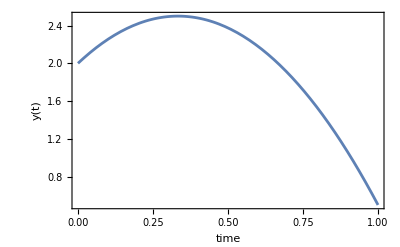

```mathematica
Plot[y[t],{t,0,1},FrameLabel->{"time","y(t)"}]
```

```mathematica
list=Table[{x[t],y[t]},{t,0,4}];
```

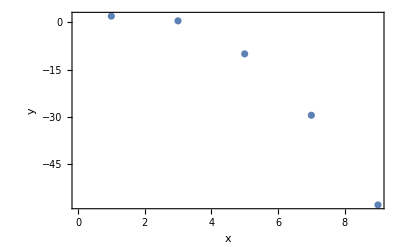

```mathematica
ListPlot[list,FrameLabel->{"x","y"}]
```

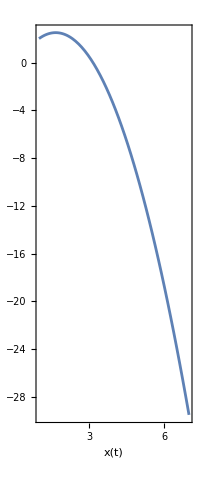

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,3},FrameLabel->{"x(t)
","y(t)"},AspectRatio->Full]
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2}, AxesLabel->{"x","y","f"}]
```

-Graphics3D-

## Example B.8

```mathematica
Remove["Global`*"]
```

```mathematica
y=y0+v0*t-1/2*g*t^2;
```

```mathematica
D[y,t]
```

-g t+v0

```mathematica
tmax=Solve[D[y,t]==0,t]
```

{{t→v0/g}}

```mathematica
y/.tmax[[1]]
```

v0^2/(2 g)+y0

## Example B.9

```mathematica
Remove["Global`*"]
```

```mathematica
force=-k*x;
```

```mathematica
Integrate[force,{x,x1,x2}]//Simplify
```

1/2 k (x1^2-x2^2)

## Example B.10

```mathematica
Remove["Global`*"]
```

```mathematica
soln=DSolve[{x''[t]==-k*x[t],x[0]==x0,x'[0]==0},x,t];
```

```mathematica
x[t]/.soln[[1]]
```

x0 Cos[√k t]